## Lista 1 - Exercício 4

### 1 Definindo o Problema

#### 1.1 Função Mapeamento

```mathematica
Clear[x, y]
```

```mathematica
f = 1/4(η-1)(ξ-1)(-η-ξ-1)
```

1/4 (-1+η) (-1-η-ξ) (-1+ξ)

#### 1.2 Parâmetros de Mapeamento

```mathematica
x = 1/4(-η ξ^2+η+ξ^2+4ξ-1)
y = 1/4(-(η^2(ξ-1))+4η+ξ-1)
```

1/4 (-1+η+4 ξ+ξ^2-η ξ^2)

1/4 (-1+4 η-η^2 (-1+ξ)+ξ)

### 2 Cálculo das Derivadas Parciais da Regra da Cadeia

Para o cálculo do gradiente, cálcula-se as derivadas parcias:

										(df(ξ,η))/dx = df/dξ dξ/dx + df/dη dη/dx
										
										 (df(ξ,η))/dy = df/dξ dξ/dy + df/dη dη/dy

 De tal forma que:
     										     ∇f = ((df(ξ,η))/dx
(df(ξ,η))/dy)

#### 2.1 df/dξ

```mathematica
dfdξ = D[f, ξ]
```

1/4 (-1+η) (-1-η-ξ)-1/4 (-1+η) (-1+ξ)

#### 2.2 df/dη

```mathematica
dfdη = D[f, η]
```

-1/4 (-1+η) (-1+ξ)+1/4 (-1-η-ξ) (-1+ξ)

#### 2.3 dx/dξ

```mathematica
dxdξ = D[x, ξ]
```

1/4 (4+2 ξ-2 η ξ)

#### 2.4 dx/dη

```mathematica
dxdη = D[x, η]
```

1/4 (1-ξ^2)

#### 2.5 dy/dξ

```mathematica
dydξ = D[y, ξ]
```

1/4 (1-η^2)

#### 2.6 dy/dη

```mathematica
dydη = D[y, η]
```

1/4 (4-2 η (-1+ξ))

### 3 Cálculo do Jacobiano

O jacobiano é utilizado para realizar a transformação do domínio (d/dξ, d/dη) para (d/dx, d/dy).

												dξ/dx=1/(|jac|)dy/dη
												
												dξ/dy=-1/(|jac|)dx/dη
												
												dη/dx=-1/(|jac|)dy/dξ
												
												dη/dy=1/(|jac|)dx/dξ

```mathematica
jacobian = ({{dxdξ, dxdη}, {dydξ, dydη}});
%//MatrixForm
```

(1/4 (4+2 ξ-2 η ξ) | 1/4 (1-ξ^2)
1/4 (1-η^2) | 1/4 (4-2 η (-1+ξ)))

```mathematica
detJac = dxdξ dydη - dxdη dydξ;
%//Simplify
```

1/16 (15+8 ξ+ξ^2-4 η (-2+3 ξ+ξ^2)+η^2 (1-4 ξ+3 ξ^2))

### 4 Derivadas Parciais nos Domínios x e y

#### 4.1 dξ/dx

```mathematica
dξdx = 1/detJac dydη;
%//Simplify
```

(8 (2+η-η ξ))/(15+8 ξ+ξ^2-4 η (-2+3 ξ+ξ^2)+η^2 (1-4 ξ+3 ξ^2))

#### 4.2 dξ/dy

```mathematica
dξdy = -1/detJac dxdη;
%//Simplify
```

(4 (-1+ξ^2))/(15+8 ξ+ξ^2-4 η (-2+3 ξ+ξ^2)+η^2 (1-4 ξ+3 ξ^2))

#### 4.3 dη/dx

```mathematica
dηdx = -1/detJac dydξ;
%//Simplify
```

(4 (-1+η^2))/(15+8 ξ+ξ^2-4 η (-2+3 ξ+ξ^2)+η^2 (1-4 ξ+3 ξ^2))

#### 4.4 dη/dy

```mathematica
dηdy = 1/detJac dxdξ;
%//Simplify
```

(8 (2+ξ-η ξ))/(15+8 ξ+ξ^2-4 η (-2+3 ξ+ξ^2)+η^2 (1-4 ξ+3 ξ^2))

### 5 Gradiente de f em relação a x e y

#### 5.1 df/dx

```mathematica
dfdx = dfdξ dξdx + dfdη dxdη;
%//Simplify
```

1/16 (-1+ξ) (2 η+ξ) (-1+ξ^2)+(2 (-1+η) (-2+η (-1+ξ)) (η+2 ξ))/(15+8 ξ+ξ^2-4 η (-2+3 ξ+ξ^2)+η^2 (1-4 ξ+3 ξ^2))

#### 5.2 df/dy

```mathematica
dfdy = dfdξ dξdy + dfdη dηdy;
%//Simplify
```

((-1+ξ) (-2 ξ+η^2 (-1+3 ξ)-η (7+5 ξ)))/(15+8 ξ+ξ^2-4 η (-2+3 ξ+ξ^2)+η^2 (1-4 ξ+3 ξ^2))

```mathematica
gradF = {dfdx, dfdy};
%//MatrixForm//Simplify
```

(1/16 (-1+ξ) (2 η+ξ) (-1+ξ^2)+(2 (-1+η) (-2+η (-1+ξ)) (η+2 ξ))/(15+8 ξ+ξ^2-4 η (-2+3 ξ+ξ^2)+η^2 (1-4 ξ+3 ξ^2))
((-1+ξ) (-2 ξ+η^2 (-1+3 ξ)-η (7+5 ξ)))/(15+8 ξ+ξ^2-4 η (-2+3 ξ+ξ^2)+η^2 (1-4 ξ+3 ξ^2)))

### 6 Resultados

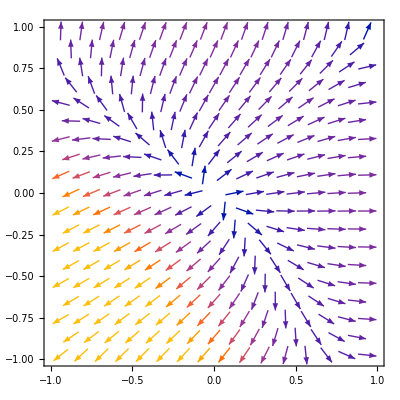

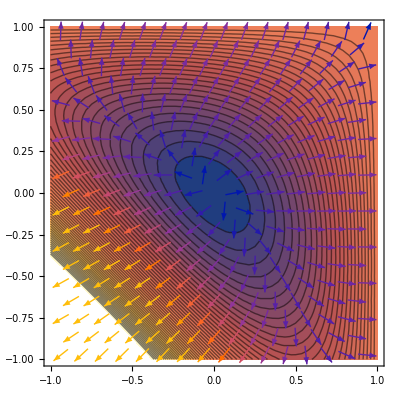

```mathematica
a=VectorPlot[gradF,  {ξ, -1, 1}, {η, -1, 1}]
b=ContourPlot[f,{ξ,-1,1},{η,-1,1},Contours->50];

Show[b, a]
```